### Figures

#### H-Tree

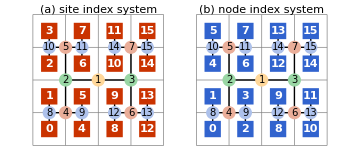

```mathematica
Block[{n=4,d=2,p,node,bgn},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{{Line[{Mean/@rng,Mean/@rng1}],p1},{Line[{Mean/@rng,Mean/@rng2}],p2},
Translate[{{EdgeForm[AbsoluteThickness[1]],Lighter[ColorData[0,Log[2,Times@@(Subtract@@@rng)]],0.6],Disk[{0,0},0.18]},Text[Style[ind,10],{0,0}]},Mean/@rng]}],
{node[<|Red->#.n^Range[d-1,0,-1],Blue->ind-n^d|>,#+1/2]&@rng⟦;;,1⟧}];
node[id_,pos_]:=Translate[{{col,Rectangle[{-0.25,-0.25},{0.25,0.25},RoundingRadius->0.12]},{White,Text[Style[id[col],Bold]]}},pos];
bgn={{Gray,AbsoluteThickness[0.5],Line[{{#,0},{#,n}}&/@Range[0,n]],Line[{{0,#},{n,#}}&/@Range[0,n]]}};
Graphics[{Translate[{bgn,Block[{col=Red},p[ConstantArray[{0,n},d],0,1]],Text["(a) site index system",{n/2,n},{0,-1}]},{-(n+1)/2,0}],Translate[{bgn,Block[{col=Blue},p[ConstantArray[{0,n},d],0,1]],Text["(b) node index system",{n/2,n},{0,-1}]},{(n+1)/2,0}]},ImageSize->360]
]
```

#### Causal Graph

```mathematica
Block[{L=4,d=2,r=1,a=0.4,h=3,h2=2.5,ecol,estyle,partition,rs,discover,graph,tree,nd,nds,nodes,map},
partition[rng_,dim_, ind_]:=Block[{mid,rng1,rng2},
If[EvenQ@Total@rng⟦dim⟧,
Sow[ind->(Mean/@rng)];
mid=Mean@rng⟦dim⟧;
{rng1,rng2}={rng,rng};
rng1⟦dim,2⟧=mid;
rng2⟦dim,1⟧=mid;
{partition[rng1,Mod[dim+1,d,1],2 ind],
partition[rng2,Mod[dim+1,d,1],2 ind+1]}]];
rs=Last/@SortBy[First]@First@Last@Reap[partition[ConstantArray[{0,L},d],1,1]];
discover[z_]:=Block[{s,t,dis},
s=rs⟦2^(z-1);;2^z-1⟧;
t=rs⟦2^z;;2^(z+1)-1⟧;
dis=Table[Norm[N@Mod[a-b,L,-L/2]],{a,s},{b,t}]/(2^(Log[2,L]-z/d));
{s,t}=Thread[First/@Most@ArrayRules@UnitStep[r-dis]]-1;
{2^(z-1)+s,2^z+t}];
graph=Block[{adj0,adj1,adj2,adj11,adj22,adj21},
adj0=SparseArray[Band[{1,1}]->1,{#,#}&@(2^L-1)];
adj1=SparseArray[Flatten[Reverse@#->1&/@Thread@discover[#]&/@Range[d Log[2,L]-1]],{#,#}&@(2^L-1)];
adj2=adj1.adj1;
adj11=LowerTriangularize[Clip[adj1.Transpose[adj1]],-1];
adj22=LowerTriangularize[Clip[adj2.Transpose[adj2]+adj11],-1]-adj11;
adj21=LowerTriangularize[Clip[adj2.Transpose[adj1]+adj1],-1]-adj1;
DeleteCases[First/@Most@ArrayRules@SparseArray[#],{a_,b_}/;a≥8||b≥8]&/@<|0->adj0,1->adj1,2->adj11,3->adj21,4->adj22,5->adj2|>];
nd[i_]:={EdgeForm[Directive[AbsoluteThickness[1],GrayLevel[0.6]]],
Lighter[Black,0.95+0.05(-1)^If[i==0,0,Floor[Log[2,i]]+1]],Rectangle[{-a,-a},{a,a},RoundingRadius->0.1a],{Black,Text[StringTemplate["\!\(z\_`1`\)"][i],{0,0}]}};
nds={EdgeForm[Directive[AbsoluteThickness[1],GrayLevel[0.6]]],Table[{Table[Translate[nd[i],{2 a i,0}],{i,Floor[2^(l-1)],2^l-1}]},{l,0,3}]};
ecol=<|0->Gray,1->Red,2->Green,3->Blue,4->Yellow,5->Purple|>;
estyle=Directive[Arrowheads[{{0.01,0.65,Graphics[Line[Offset/@{{-4,2},{0,0},{-4,-2}}]]}}],
Opacity[0.8],AbsoluteThickness[1.5]];
tree=Block[{depth=4},nodes=Association@Prepend[Flatten@Table[{Table[i->{2^(depth-l)(i-2^(l-1)+FractionalPart[2^(l-1)]/2+1/2),-h2 l},{i,Floor[2^(l-1)],2^l-1}]},{l,1,depth-1}],0->{4,-1.5}];
{{Table[{estyle,ecol[typ],
Table[Block[{s,t},
{t,s}=edge;
Switch[edge,{4|7,1},Arrow[BSplineCurve@{nodes[s],(nodes[s]+nodes[t])/2+0.2{First[nodes[s]-nodes[t]],0},nodes[t]}],
{6,4}|{7,5},Arrow[BSplineCurve@{nodes[s],(nodes[s]+nodes[t])/2-{0,1.5},nodes[t]}],
{7,4},Arrow[BSplineCurve@{nodes[s],(nodes[s]+nodes[t])/2-{0,2.5},nodes[t]}],
_,Arrow[{nodes[s],nodes[t]}]]],{edge,graph[typ]}]},{typ,5}]},
Translate[nd[#],nodes[#]]&/@Range[0,7]}];
map[typ0_]:=Table[{estyle,If[typ>2,Opacity[0.2]],ecol[typ],Arrow@BSplineCurve[{{2a#2,a},{2a#2,2a},{2a#1,h-2a},{2a#1,h-a}}]&@@@graph[typ]},{typ,typ0,5}];
Row@{Graphics[{tree,Text["(a)",{1,-1},{-1,1}]},PlotRange->{{0,8},{-9,-1}},ImageSize->{Automatic,150}],
Graphics[{{map[1],Translate[map[0],{0,h}]},Translate[nds,{0,# h}]&/@Range[0,2],Text["(b)",{7a,2h+2a}]},ImageSize->{Automatic,150}],
Grid[{Graphics[{{estyle,#,Arrow[{{0,0},{1,0}}]}},AspectRatio->0.2,ImageSize->22],Graphics[Text[Style[#2,12,FontFamily->"CMU"]],AspectRatio->0.01,ImageSize->60]}&@@@Thread@{Values@ecol,{"self","child","sibling","niephew","cousin","grandchild"}},Spacings->{0.2,-0.3}]}]
```

-Graphics--Graphics--Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

### Backup

#### Heap Linear Layer

```mathematica
Block[{L=8,a=0.5,h=4,h2=2.5,d,nd,nds,map,hl,tree},
d=Ceiling[Log[2,L]]+1;
nd[i_]:={Rectangle[{-a,-a},{a,a},RoundingRadius->0.1a],{Black,Text[StringTemplate["\!\(x\_`1`\)"][i],{0,0}]}};
nds={EdgeForm[Directive[AbsoluteThickness[1],GrayLevel[0.6]]],Table[{Lighter[ColorData[0][l],0.95-0.05l],Table[Translate[nd[i],{i,0}],{i,Floor[2^(l-1)],2^l-1}]},{l,0,d-1}]};
map[i_,j_]:=Arrow[BSplineCurve[{{i,a},{i,2a},{(i+j)/2,h/2},{j,h-2a},{j,h-a}}]];
hl[k0_]:={Arrowheads[{{0.01,0.9,Graphics[Line[Offset/@{{-4,2},{0,0},{-4,-2}}]]}}],
Table[{ColorData[0][k],Opacity[0.6],
Table[Block[{i0,i1},
i0=Floor[2^(l-1)];
i1=2^l;
Table[Block[{j0,j1},
If[i==0,
j0=Floor[2^(k-1)];
j1=Floor[2^(k-1)]+Ceiling[2^(k-1)],
j0=i 2^k;
j1=(i+1) 2^k];
Table[If[j1≤L,map[i,j],Nothing],
{j,j0,j1-1}]],{i,i0,i1-1}]],
{l,0,d-1}]},
{k,k0,d-1}]};
tree={{Arrowheads[{{0.01,0.5,Graphics[Line[Offset/@{{-4,2},{0,0},{-4,-2}}]]}}],Table[{Table[Translate[Table[Arrow[{{0,0},{2^(d-l-1)(q-1/2),-h2}}],{q,If[l==0,{1/2},{0,1}]}],{2^(d-l)(i-2^(l-1)+FractionalPart[2^(l-1)]/2+1/2),-h2 l}],{i,Floor[2^(l-1)],2^l-1}]},{l,0,d-2}]},{EdgeForm[Directive[AbsoluteThickness[1],GrayLevel[0.6]]],Table[{Lighter[ColorData[0][l],0.95-0.05l],Table[Translate[nd[i],{2^(d-l)(i-2^(l-1)+FractionalPart[2^(l-1)]/2+1/2),-h2 l}],{i,Floor[2^(l-1)],2^l-1}]},{l,0,d-1}]}};
Graphics[{Translate[#1,{0,#2h}]&@@@Thread@{{hl[1],hl[0]},{0,1}},
Translate[nds,{0,# h}]&/@Range[0,2],Text["(b)",{-1.2,8}],
Translate[{tree,Text["(a)",{1,0.5}]},{-9,7.5}]},ImageSize->260]]
```

-Graphics-

```mathematica
Block[{L=8,a=0.5,h=4,h2=2.5,d,nd,nds,map,hl,tree},
d=Ceiling[Log[2,L]]+1;
nd[i_,l_]:={Lighter[ColorData[0][l],0.95-0.05l],Rectangle[{-a,-a},{a,a},RoundingRadius->0.1a],{Black,Text[StringTemplate["\!\(z\_`1`\)"][i],{0,0}]}};
nds={EdgeForm[Directive[AbsoluteThickness[1],GrayLevel[0.6]]],Table[{Table[Translate[nd[i,l],{i,0}],{i,Floor[2^(l-1)],2^l-1}]},{l,0,d-1}]};
map[i_,j_]:=Arrow[BSplineCurve[{{i,a},{i,2a},{(i+j)/2,h/2},{j,h-2a},{j,h-a}}]];
hl[k0_]:={Arrowheads[{{0.01,0.78,Graphics[Line[Offset/@{{-4,2},{0,0},{-4,-2}}]]}}],
Opacity[0.8],AbsoluteThickness[1.5],
Table[
Table[Block[{i0,i1},
i0=Floor[2^(l-1)];
i1=2^l;
Table[Block[{j0,j1},
j0=i 2^k;
j1=(i+1) 2^k;
Table[If[j1≤L,{If[k==0,GrayLevel[0.6],
ColorData[0][2l+(j-i 2^k)-1]],map[i,j]},Nothing],
{j,j0,j1-1}]],{i,i0,i1-1}]],
{l,1,d-1}],
{k,k0,1(*d-1*)}]};
tree={{Arrowheads[{{0.01,0.5,Graphics[Line[Offset/@{{-4,2},{0,0},{-4,-2}}]]}}],
Opacity[0.8],AbsoluteThickness[1.5],Table[{Table[Translate[Table[{ColorData[0][Mod[2l+q-1,5]],Arrow[{{0,0},{2^(d-l-1)(q-1/2),-h2}}]},{q,{0,1}}],{2^(d-l)(i-2^(l-1)+FractionalPart[2^(l-1)]/2+1/2),-h2 l}],{i,Floor[2^(l-1)],2^l-1}]},{l,1,d-2}]},{EdgeForm[Directive[AbsoluteThickness[1],GrayLevel[0.6]]],Table[{Table[Translate[nd[i,l],{2^(d-l)(i-2^(l-1)+FractionalPart[2^(l-1)]/2+1/2),-h2 l}],{i,Floor[2^(l-1)],2^l-1}]},{l,0,d-1}]}};
Graphics[{Translate[#1,{0,#2h}]&@@@Thread@{{hl[1],hl[0]},{0,1}},
Translate[nds,{0,# h}]&/@Range[0,2],Text["(b)",{-1.2,8}],
Translate[{tree,Text["(a)",{1,0.5}]},{-9,7.5}]},ImageSize->260]]
```

-Graphics-

#### Free Energy Benchmark

```mathematica
Block[{L=4,J=0.440686793,xs,eng},
xs=ArrayReshape[Tuples[{-1,1},L^2],{2^(L^2),L,L}];
eng[x_]:=-J Total@Flatten[x RotateLeft[x,{1,0}]+x RotateLeft[x,{0,1}]];
-Log@Total@Exp[-eng/@xs]]
```

-15.5219

```mathematica
Block[{L=4,J=0.2,xs,eng},
xs=ArrayReshape[Tuples[{-1,1},L^2],{2^(L^2),L,L}];
eng[x_]:=-J Total@Flatten[x RotateLeft[x,{1,0}]+x RotateLeft[x,{0,1}]];
-Log@Total@Exp[-eng/@xs]]
```

-11.7715

```mathematica
Block[{L=2,J=0.7,xs,eng,es,ps},
xs=ArrayReshape[Tuples[{-1,1},L^2],{2^(L^2),L,L}];
eng[x_]:=-J Total@Flatten[x RotateLeft[x,{1,0}]+x RotateLeft[x,{0,1}]];
es=eng/@xs;
ps=#/Total[#]&@Exp[-es];
Print[-Log@Total@Exp[-eng/@xs]];
Column@Thread[Range[0,Length@ps-1]->ps]]
```

-6.31511

0→0.489141
1→0.00180878
2→0.00180878
3→0.00180878
4→0.00180878
5→0.00180878
6→6.68861×10^-6
7→0.00180878
8→0.00180878
9→6.68861×10^-6
10→0.00180878
11→0.00180878
12→0.00180878
13→0.00180878
14→0.00180878
15→0.489141

```mathematica
Block[{L=2,J=0.7,zs,eng,es,ps},
zs=Tuples[{-1,1},L^2];
eng[z_]:=-2J (z⟦2⟧+z⟦3⟧+z⟦4⟧+z⟦2⟧z⟦3⟧z⟦4⟧);
es=eng/@zs;
ps=#/Total[#]&@Exp[-es];
Print[-Log@Total@Exp[-eng/@zs]];
Column@Thread[Range[0,Length@ps-1]->ps]]
```

-5.07025

0→0.0000941854
1→0.00154885
2→0.00154885
3→0.0254702
4→0.00154885
5→0.0254702
6→0.0254702
7→0.418849
8→0.0000941854
9→0.00154885
10→0.00154885
11→0.0254702
12→0.00154885
13→0.0254702
14→0.0254702
15→0.418849

#### 2D Fractal

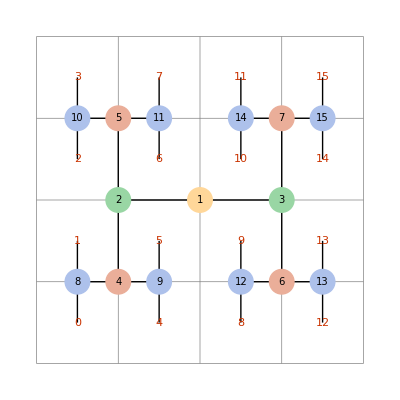

```mathematica
Block[{n=4,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{{Line[{Mean/@rng,Mean/@rng1}],p1},{Line[{Mean/@rng,Mean/@rng2}],p2},
Translate[{{EdgeForm[AbsoluteThickness[1]],Lighter[ColorData[0,Log[2,Times@@(Subtract@@@rng)]],0.6],Disk[{0,0},0.15]},Text[Style[ind,10],{0,0}]},Mean/@rng]}],
{Red,Translate[Text[#.n^Range[d-1,0,-1]],#+{1,1}/2]&@rng⟦;;,1⟧}];
Graphics[{{Gray,AbsoluteThickness[0.5],Line[{{#,0},{#,n}}&/@Range[0,n]],Line[{{0,#},{n,#}}&/@Range[0,n]]},{p[ConstantArray[{0,n},d],0,1]}}]]
```

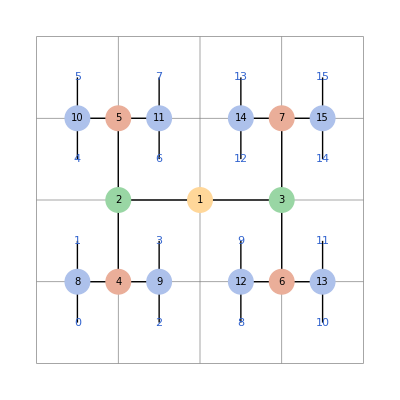

```mathematica
Block[{n=4,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{{Line[{Mean/@rng,Mean/@rng1}],p1},{Line[{Mean/@rng,Mean/@rng2}],p2},
Translate[{{EdgeForm[AbsoluteThickness[1]],Lighter[ColorData[0,Log[2,Times@@(Subtract@@@rng)]],0.6],Disk[{0,0},0.15]},Text[Style[ind,10],{0,0}]},Mean/@rng]}],
{Blue,Translate[Text[ind-n^d],#+{1,1}/2]&@rng⟦;;,1⟧}];
Graphics[{{Gray,AbsoluteThickness[0.5],Line[{{#,0},{#,n}}&/@Range[0,n]],Line[{{0,#},{n,#}}&/@Range[0,n]]},{p[ConstantArray[{0,n},d],0,1]}}]]
```

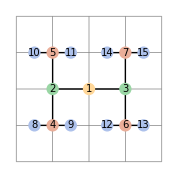

```mathematica
Block[{n=4,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{If[p1=!={},{Line[{Mean/@rng,Mean/@rng1}],p1},Nothing],If[p2=!={},{Line[{Mean/@rng,Mean/@rng2}],p2},Nothing],
Translate[{{EdgeForm[AbsoluteThickness[1]],Lighter[ColorData[0,Log[2,Times@@(Subtract@@@rng)]],0.6],Disk[{0,0},0.15]},Text[Style[ind,10],{0,0}]},Mean/@rng]}],
{}];
Graphics[{{Gray,AbsoluteThickness[0.5],Line[{{#,0},{#,n}}&/@Range[0,n]],Line[{{0,#},{n,#}}&/@Range[0,n]]},{p[ConstantArray[{0,n},d],0,1]}}]]
```

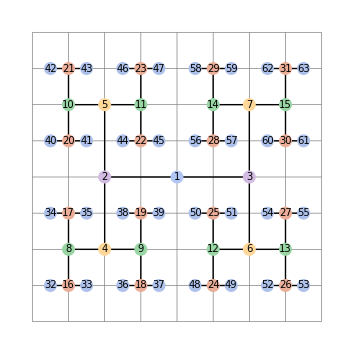

```mathematica
Block[{n=8,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{If[p1=!={},{Line[{Mean/@rng,Mean/@rng1}],p1},Nothing],If[p2=!={},{Line[{Mean/@rng,Mean/@rng2}],p2},Nothing],
Translate[{{EdgeForm[AbsoluteThickness[1]],Lighter[ColorData[0,Log[2,Times@@(Subtract@@@rng)]],0.6],Disk[{0,0},0.16]},Text[Style[ind,10],{0,0}]},Mean/@rng]}],
{}];
Graphics[{{Gray,AbsoluteThickness[0.5],Line[{{#,0},{#,n}}&/@Range[0,n]],Line[{{0,#},{n,#}}&/@Range[0,n]]},{p[ConstantArray[{0,n},d],0,1]}}]]
```

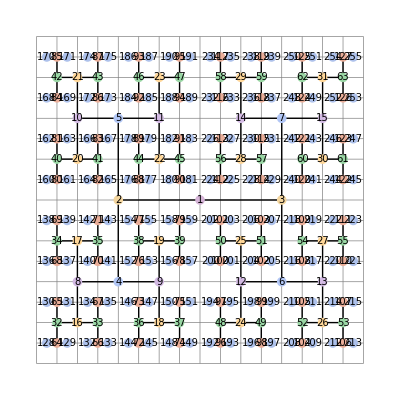

```mathematica
Block[{n=16,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{If[p1=!={},{Line[{Mean/@rng,Mean/@rng1}],p1},Nothing],If[p2=!={},{Line[{Mean/@rng,Mean/@rng2}],p2},Nothing],
Translate[{{EdgeForm[AbsoluteThickness[1]],Lighter[ColorData[0,Log[2,Times@@(Subtract@@@rng)]],0.6],Disk[{0,0},0.2]},Text[Style[ind,10],{0,0}]},Mean/@rng]}],
{}];
Graphics[{{Gray,AbsoluteThickness[0.5],Line[{{#,0},{#,n}}&/@Range[0,n]],Line[{{0,#},{n,#}}&/@Range[0,n]]},{p[ConstantArray[{0,n},d],0,1]}}]]
```

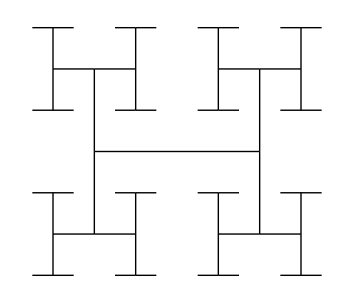

```mathematica
Block[{n=8,d=2,p},
p[rng_,dim_,ind_]:=
If[EvenQ@Total@rng⟦dim+1⟧,
Block[{mid=Total@rng⟦dim+1⟧/2,rng1,rng2,p1,p2},
rng1=rng;rng2=rng;
rng1⟦dim+1,2⟧=mid;
rng2⟦dim+1,1⟧=mid;
p1=p[rng1,Mod[dim+1,d],2 ind];
p2=p[rng2,Mod[dim+1,d],2 ind+1];
{If[p1=!={},{Line[{Mean/@rng,Mean/@rng1}],p1},Nothing],If[p2=!={},{Line[{Mean/@rng,Mean/@rng2}],p2},Nothing],{}}],
{}];
Graphics[{p[ConstantArray[{0,n},d],0,1]}]]
```

#### RG and Haar Transform

```mathematica
Block[{gs},
gs=Subscript[g,#]&/@Range[0,15];
Do[Do[{gs⟦2q+1⟧=gs⟦q+1⟧,gs⟦2q+2⟧=gs⟦2^(z-1)+q+1⟧∘gs⟦q+1⟧},{q,0,2^(z-1)-1}],{z,1,1}];
gs]
```

{g_0,g_1∘g_0,g_2,g_3,g_4,g_5,g_6,g_7,g_8,g_9,g_10,g_11,g_12,g_13,g_14,g_15}

```mathematica
Block[{gs},
gs=Subscript[g,#]&/@Range[0,15];
Do[Do[{gs⟦2q+1⟧=gs⟦q+1⟧,gs⟦2q+2⟧=gs⟦2^(z-1)+q+1⟧∘gs⟦q+1⟧},{q,0,2^(z-1)-1}],{z,1,2}];
gs]
```

{g_0,g_2∘g_0,g_2∘g_0,g_3∘(g_2∘g_0),g_4,g_5,g_6,g_7,g_8,g_9,g_10,g_11,g_12,g_13,g_14,g_15}

```mathematica
Block[{gs,ζ,z=1,fs},
gs=Subscript[g,#]&/@Range[0,15];
fs=gs;
ζ=Log[2,Length@gs]+1;
Table[Do[fs⟦q+1⟧=gs⟦2q+1⟧;fs⟦2^(ζ-1-z)+q+1⟧=gs⟦2q+1⟧^(-1)gs⟦2q+2⟧;,{q,0,2^(ζ-1-z)-1}];gs=fs,{z,1,ζ-1}]]
```

{{g_0,g_2,g_4,g_6,g_8,g_10,g_12,g_14,g_1/g_0,g_3/g_2,g_5/g_4,g_7/g_6,g_9/g_8,g_11/g_10,g_13/g_12,g_15/g_14},{g_0,g_4,g_8,g_12,g_2/g_0,g_6/g_4,g_10/g_8,g_14/g_12,g_1/g_0,g_3/g_2,g_5/g_4,g_7/g_6,g_9/g_8,g_11/g_10,g_13/g_12,g_15/g_14},{g_0,g_8,g_4/g_0,g_12/g_8,g_2/g_0,g_6/g_4,g_10/g_8,g_14/g_12,g_1/g_0,g_3/g_2,g_5/g_4,g_7/g_6,g_9/g_8,g_11/g_10,g_13/g_12,g_15/g_14},{g_0,g_8/g_0,g_4/g_0,g_12/g_8,g_2/g_0,g_6/g_4,g_10/g_8,g_14/g_12,g_1/g_0,g_3/g_2,g_5/g_4,g_7/g_6,g_9/g_8,g_11/g_10,g_13/g_12,g_15/g_14}}

```mathematica
Block[{ζ=5},
Table[Table[2^(z-1)+q-> 2^(ζ-1-z){2q+1,2q+2},{q,0,2^(z-1)-1}],{z,1,ζ-1}]]
```

{{1→{8,16}},{2→{4,8},3→{12,16}},{4→{2,4},5→{6,8},6→{10,12},7→{14,16}},{8→{1,2},9→{3,4},10→{5,6},11→{7,8},12→{9,10},13→{11,12},14→{13,14},15→{15,16}}}

```mathematica
Block[{gs,ζ,z=1},
gs=Subscript[g,#]&/@Range[0,15];
ζ=Log[2,Length@gs]+1;
Table[gs =Normal@SparseArray[Flatten@Table[{{q+1}->gs⟦2q+1⟧,{2^(ζ-1-z)+q+1}->gs⟦2q+1⟧^(-1)gs⟦2q+2⟧},{q,0,2^(ζ-1-z)-1}],16],{z,1,2}]]
```

{{g_0,g_2,g_4,g_6,g_8,g_10,g_12,g_14,g_1/g_0,g_3/g_2,g_5/g_4,g_7/g_6,g_9/g_8,g_11/g_10,g_13/g_12,g_15/g_14},{g_0,g_4,g_8,g_12,g_2/g_0,g_6/g_4,g_10/g_8,g_14/g_12,0,0,0,0,0,0,0,0}}

```mathematica
SparseArray[{1->1}]
```

SparseArray[…]

```mathematica
List@@SparseArray[{1->1,2->1},{16}]
```

{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### NodeVect

-Graphics-

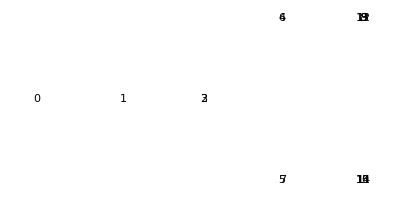

```mathematica
Block[{vs,u,w,v},
{vs}=Import[FileNameJoin[{NotebookDirectory[],"data","nodevec.json"}]];
Print@ComplexMatrixPlot@vs;
{u,w,v}=SingularValueDecomposition[vs];
Graphics[Text[#1-1,#2]&@@@Thread@{Range[Length@vs],(vs.v)⟦All,{1,2}⟧}]]
```